```mathematica
SqrtMod[a_,n_]:=(Module[{i,x,points,A,N},
points={};
A=a;N=n;
For[A=0,A<N,A++,
For[x=0,x<N,x++,
If[Mod[x^2,N]==A, points=Append[points,{x,A}]]
]
];
(*Entrega los resultados*)
Print[points];
Return[Graphics[{PointSize[Small],Blue,Point[points]},Axes->True]];
]
)
```

{{0,0},{1,1},{32,1},{340,1},{373,1},{650,1},{683,1},{991,1},{1022,1},{2,4},{64,4},{277,4},{343,4},{680,4},{746,4},{959,4},{1021,4},{3,9},{96,9},{927,9},{1020,9},{4,16},{128,16},{337,16},{469,16},{554,16},{686,16},{895,16},{1019,16},{5,25},{160,25},{181,25},{346,25},{677,25},{842,25},{863,25},{1018,25},{124,31},{217,31},{806,31},{899,31},{132,33},{891,33},{6,36},{192,36},{831,36},{1017,36},{111,45},{483,45},{540,45},{912,45},{7,49},{224,49},{334,49},{458,49},{565,49},{689,49},{799,49},{1016,49},{8,64},{85,64},{256,64},{349,64},{674,64},{767,64},{938,64},{1015,64},{33,66},{990,66},{56,67},{254,67},{397,67},{428,67},{595,67},{626,67},{769,67},{967,67},{72,69},{258,69},{765,69},{951,69},{46,70},{233,70},{295,70},{449,70},{574,70},{728,70},{790,70},{977,70},{120,78},{252,78},{771,78},{903,78},{9,81},{288,81},{735,81},{1014,81},{136,82},{205,82},{260,82},{422,82},{601,82},{763,82},{818,82},{887,82},{279,93},{744,93},{91,97},{157,97},{184,97},{250,97},{773,97},{839,97},{866,97},{932,97},{10,100},{320,100},{331,100},{362,100},{661,100},{692,100},{703,100},{1013,100},{369,102},{468,102},{555,102},{654,102},{79,103},{200,103},{262,103},{482,103},{541,103},{761,103},{823,103},{944,103},{210,111},{441,111},{582,111},{813,111},{11,121},{352,121},{671,121},{1012,121},{248,124},{434,124},{589,124},{775,124},{147,126},{411,126},{612,126},{876,126},{264,132},{759,132},{34,133},{65,133},{307,133},{406,133},{617,133},{716,133},{958,133},{989,133},{12,144},{384,144},{639,144},{1011,144},{116,157},{302,157},{380,157},{457,157},{566,157},{643,157},{721,157},{907,157},{246,159},{312,159},{711,159},{777,159},{47,163},{140,163},{388,163},{481,163},{542,163},{635,163},{883,163},{976,163},{231,165},{792,165},{13,169},{266,169},{328,169},{416,169},{607,169},{695,169},{757,169},{1010,169},{102,174},{195,174},{828,174},{921,174},{57,180},{222,180},{801,180},{966,180},{154,187},{187,187},{836,187},{869,187},{215,190},{281,190},{401,190},{467,190},{556,190},{622,190},{742,190},{808,190},{14,196},{107,196},{355,196},{448,196},{575,196},{668,196},{916,196},{1009,196},{35,202},{97,202},{244,202},{376,202},{647,202},{779,202},{926,202},{988,202},{73,214},{268,214},{290,214},{392,214},{631,214},{733,214},{755,214},{950,214},{15,225},{480,225},{543,225},{1008,225},{297,231},{726,231},{86,235},{317,235},{365,235},{427,235},{596,235},{658,235},{706,235},{937,235},{242,253},{440,253},{583,253},{781,253},{16,256},{170,256},{325,256},{511,256},{512,256},{698,256},{853,256},{1007,256},{48,258},{510,258},{513,258},{975,258},{80,262},{173,262},{421,262},{509,262},{514,262},{602,262},{850,262},{943,262},{66,264},{957,264},{270,267},{456,267},{567,267},{753,267},{112,268},{167,268},{229,268},{508,268},{515,268},{794,268},{856,268},{911,268},{36,273},{129,273},{894,273},{987,273},{144,276},{507,276},{516,276},{879,276},{372,279},{651,279},{92,280},{125,280},{433,280},{466,280},{557,280},{590,280},{898,280},{931,280},{176,286},{506,286},{517,286},{847,286},{17,289},{203,289},{358,289},{479,289},{544,289},{665,289},{820,289},{1006,289},{58,295},{151,295},{190,295},{283,295},{740,295},{833,295},{872,295},{965,295},{396,297},{627,297},{133,298},{164,298},{208,298},{505,298},{518,298},{815,298},{859,298},{890,298},{240,312},{504,312},{519,312},{783,312},{121,319},{220,319},{803,319},{902,319},{18,324},{447,324},{576,324},{1005,324},{179,328},{272,328},{410,328},{503,328},{520,328},{613,328},{751,328},{844,328},{198,330},{825,330},{309,342},{342,342},{681,342},{714,342},{339,345},{405,345},{618,345},{684,345},{37,346},{161,346},{304,346},{502,346},{521,346},{719,346},{862,346},{986,346},{49,355},{137,355},{292,355},{478,355},{545,355},{731,355},{886,355},{974,355},{213,357},{345,357},{678,357},{810,357},{19,361},{74,361},{322,361},{415,361},{608,361},{701,361},{949,361},{1004,361},{336,366},{501,366},{522,366},{687,366},{465,372},{558,372},{103,379},{227,379},{238,379},{455,379},{568,379},{785,379},{796,379},{920,379},{182,388},{314,388},{368,388},{500,388},{523,388},{655,388},{709,388},{841,388},{117,390},{348,390},{675,390},{906,390},{67,397},{98,397},{274,397},{439,397},{584,397},{749,397},{925,397},{956,397},{20,400},{299,400},{361,400},{383,400},{640,400},{662,400},{724,400},{1003,400},{333,405},{426,405},{597,405},{690,405},{87,408},{285,408},{738,408},{936,408},{108,411},{387,411},{636,411},{915,411},{59,412},{158,412},{400,412},{499,412},{524,412},{623,412},{865,412},{964,412},{38,421},{148,421},{193,421},{379,421},{644,421},{830,421},{875,421},{985,421},{81,423},{477,423},{546,423},{942,423},{432,438},{498,438},{525,438},{591,438},{21,441},{351,441},{672,441},{1002,441},{141,444},{420,444},{603,444},{882,444},{50,454},{236,454},{391,454},{446,454},{577,454},{632,454},{787,454},{973,454},{330,462},{693,462},{93,465},{930,465},{185,466},{218,466},{464,466},{497,466},{526,466},{559,466},{805,466},{838,466},{276,474},{375,474},{648,474},{747,474},{22,484},{319,484},{704,484},{1001,484},{113,493},{206,493},{454,493},{476,493},{547,493},{569,493},{817,493},{910,493},{155,496},{496,496},{527,496},{868,496},{39,498},{225,498},{798,498},{984,498},{201,504},{294,504},{729,504},{822,504},{75,510},{354,510},{669,510},{948,510},{495,528},{528,528},{23,529},{287,529},{364,529},{395,529},{628,529},{659,529},{736,529},{1000,529},{60,531},{126,531},{897,531},{963,531},{68,532},{130,532},{211,532},{409,532},{614,532},{812,532},{893,532},{955,532},{234,537},{327,537},{696,537},{789,537},{306,543},{438,543},{585,543},{717,543},{51,555},{414,555},{609,555},{972,555},{278,559},{311,559},{371,559},{404,559},{619,559},{652,559},{712,559},{745,559},{122,562},{188,562},{463,562},{494,562},{529,562},{560,562},{835,562},{901,562},{134,565},{145,565},{196,565},{475,565},{548,565},{827,565},{878,565},{889,565},{24,576},{255,576},{768,576},{999,576},{40,577},{257,577},{301,577},{425,577},{598,577},{722,577},{766,577},{983,577},{88,583},{253,583},{770,583},{935,583},{82,586},{104,586},{259,586},{445,586},{578,586},{764,586},{919,586},{941,586},{99,594},{924,594},{171,597},{357,597},{666,597},{852,597},{152,598},{251,598},{431,598},{493,598},{530,598},{592,598},{772,598},{871,598},{168,603},{261,603},{762,603},{855,603},{174,609},{453,609},{570,609},{849,609},{216,621},{249,621},{774,621},{807,621},{25,625},{118,625},{223,625},{316,625},{707,625},{800,625},{905,625},{998,625},{165,627},{858,627},{109,628},{232,628},{263,628},{419,628},{604,628},{760,628},{791,628},{914,628},{138,630},{324,630},{699,630},{885,630},{399,636},{492,636},{531,636},{624,636},{177,639},{474,639},{549,639},{846,639},{61,652},{94,652},{247,652},{280,652},{743,652},{776,652},{929,652},{962,652},{41,658},{52,658},{289,658},{382,658},{641,658},{734,658},{971,658},{982,658},{462,660},{561,660},{76,661},{265,661},{296,661},{386,661},{637,661},{727,661},{758,661},{947,661},{69,669},{162,669},{861,669},{954,669},{26,676},{191,676},{367,676},{491,676},{532,676},{656,676},{832,676},{997,676},{341,682},{682,682},{180,687},{378,687},{645,687},{843,687},{245,691},{338,691},{344,691},{437,691},{586,691},{679,691},{685,691},{778,691},{204,696},{390,696},{633,696},{819,696},{267,702},{360,702},{663,702},{756,702},{209,715},{473,715},{550,715},{814,715},{149,718},{335,718},{347,718},{490,718},{533,718},{676,718},{688,718},{874,718},{114,720},{444,720},{579,720},{909,720},{142,727},{199,727},{230,727},{452,727},{571,727},{793,727},{824,727},{881,727},{27,729},{159,729},{864,729},{996,729},{243,738},{408,738},{615,738},{780,738},{42,741},{321,741},{702,741},{981,741},{308,748},{374,748},{649,748},{715,748},{83,751},{269,751},{413,751},{424,751},{599,751},{610,751},{754,751},{940,751},{183,753},{282,753},{741,753},{840,753},{89,760},{221,760},{430,760},{461,760},{562,760},{593,760},{802,760},{934,760},{303,762},{489,762},{534,762},{720,762},{53,763},{332,763},{350,763},{394,763},{629,763},{673,763},{691,763},{970,763},{62,775},{403,775},{620,775},{961,775},{28,784},{127,784},{214,784},{313,784},{710,784},{809,784},{896,784},{995,784},{100,793},{131,793},{241,793},{472,793},{551,793},{782,793},{892,793},{923,793},{105,795},{291,795},{732,795},{918,795},{123,807},{156,807},{867,807},{900,807},{70,808},{194,808},{271,808},{488,808},{535,808},{752,808},{829,808},{953,808},{77,814},{418,814},{605,814},{946,814},{363,825},{660,825},{43,826},{298,826},{329,826},{353,826},{670,826},{694,826},{725,826},{980,826},{135,834},{228,834},{795,834},{888,834},{186,837},{837,837},{29,841},{95,841},{370,841},{436,841},{587,841},{653,841},{928,841},{994,841},{110,847},{451,847},{572,847},{913,847},{146,856},{239,856},{443,856},{487,856},{536,856},{580,856},{784,856},{877,856},{119,862},{284,862},{398,862},{460,862},{563,862},{625,862},{739,862},{904,862},{54,870},{318,870},{705,870},{969,870},{273,873},{471,873},{552,873},{750,873},{30,900},{63,900},{960,900},{993,900},{153,903},{219,903},{804,903},{870,903},{207,906},{486,906},{537,906},{816,906},{139,907},{202,907},{326,907},{356,907},{667,907},{697,907},{821,907},{884,907},{44,913},{385,913},{638,913},{979,913},{84,918},{381,918},{642,918},{939,918},{429,924},{594,924},{237,927},{423,927},{600,927},{786,927},{90,939},{189,939},{834,939},{933,939},{169,940},{172,940},{293,940},{389,940},{634,940},{730,940},{851,940},{854,940},{275,946},{407,946},{616,946},{748,946},{71,949},{115,949},{226,949},{412,949},{611,949},{797,949},{908,949},{952,949},{212,955},{305,955},{377,955},{470,955},{553,955},{646,955},{718,955},{811,955},{166,958},{175,958},{197,958},{485,958},{538,958},{826,958},{848,958},{857,958},{31,961},{310,961},{713,961},{992,961},{366,966},{459,966},{564,966},{657,966},{78,969},{450,969},{573,969},{945,969},{55,979},{286,979},{737,979},{968,979},{402,993},{435,993},{588,993},{621,993},{101,994},{163,994},{178,994},{442,994},{581,994},{845,994},{860,994},{922,994},{300,999},{393,999},{630,999},{723,999},{45,1002},{417,1002},{606,1002},{978,1002},{106,1006},{235,1006},{323,1006},{359,1006},{664,1006},{700,1006},{788,1006},{917,1006},{143,1012},{484,1012},{539,1012},{880,1012},{150,1017},{315,1017},{708,1017},{873,1017}}

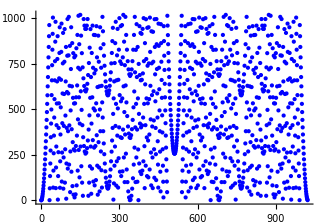

```mathematica
SqrtMod[a,1023]
```